## Cauchy distribution

### Generating Data

```mathematica
(*Common for all*)
A1 = 1;
A10 = 10;
```

```mathematica
(*x = A + CauchyDistribution[0,γ]*)
Subscript[C, g] = 1.78;
γ = (2*Subscript[C, g])^0.5;
Print["A random number from random Variate function function using Cauchy Dist : "]
RandomVariate[CauchyDistribution[0,γ]]
```

A random number from random Variate function function using Cauchy Dist :

-1.07331

```mathematica
(* Genearting data for N = 1, 10, ...*)
SampleSize = {1,10,100,1000,10000};

(*For A = 1*)
Samples1 = Table[ Table[A1 + RandomVariate[CauchyDistribution[0,γ]], {i,SampleSize[[j]]}], {j,Length[SampleSize]} ];

(*For A = 10*)
Samples10 = Table[ Table[A10 + RandomVariate[CauchyDistribution[0,γ]], {i,SampleSize[[j]]}], {j,Length[SampleSize]} ];
```

```mathematica
(*Analysing the sample using Newton Raphson*)
H1 = θ1;
```

```mathematica
(*Defining the Likelyhood function*)
ind = 5;
(*Loss1 = SUM[Log[PDF[CauchyDistribution[0,γ], (Samples1[[ind]][[i]] - H1)]], {i,SampleSize[[ind]]}];*)
g1 = Sum[D[Log[PDF[CauchyDistribution[0,γ], (Samples10[[ind]][[i]] - H1)]],H1], {i,SampleSize[[ind]]}];
dg1 = D[g1, H1];
```

```mathematica
InitialGuess = Median[Samples10[[ind]]];
For[i=0, i<5, i++, InitialGuess = InitialGuess - (g1/dg1)/.θ1->InitialGuess];
InitialGuess
```

10.0421

```mathematica
(* Full iteration *)
GetEstimateCauchy[A_, n_] := (
samples = Table[A + RandomVariate[CauchyDistribution[0,γ]], {i,n}];
AInit = Median[samples];
grad = Sum[D[Log[PDF[CauchyDistribution[0,γ], (samples[[i]] - θ)]], θ], {i,n}];
δgrad = D[grad,θ];
For[i=0, i<5, i++, AInit = AInit - (grad/δgrad)/.θ->AInit];
Return[AInit];
);
```

```mathematica
SampleSize = {1,10,100,1000,10000};
Cauchy10 = Table[  Table[ GetEstimateCauchy[10,SampleSize[[j]]] , {n_iters, 10}] , {j, Length[SampleSize]} ]
```

{{7.19566,9.77001,6.64954,10.0557,38.5667,11.7576,11.8132,12.2465,12.66,9.08418},{10.5039,10.1396,8.92616,9.58761,9.78465,10.3803,10.0093,10.9926,7.96085,10.5163},{9.83633,9.99735,10.2753,10.0129,10.132,10.0914,10.0698,9.70031,10.3723,9.92412},{10.0201,10.0328,9.98233,10.1214,10.1355,10.043,9.7763,9.94464,10.1211,9.93347},{9.96805,9.98888,9.97955,10.0037,9.98257,10.0074,9.97329,9.9702,10.0116,10.0119}}

```mathematica
Mean[Cauchy10[[1]]] 
Variance[Cauchy10[[1]]]
```

12.9799

85.0823

```mathematica
Table[{Mean[x],Variance[x]}, {x,Cauchy10}]
```

{{12.9799,85.0823},{9.88012,0.783757},{10.0412,0.0389567},{10.0111,0.0119673},{9.98972,0.000306282}}

```mathematica
Cauchy1 = Import["D:\\DISK S\\IITM\\Sem-8\\Estimation Theory\\Mini project - 1\\Cauchy1.csv"];
Table[{Mean[x],Variance[x]} , {x,Cauchy1}]
```

{{1.07615,0.0536208},{0.869952,0.159601},{1.00812,0.00114554},{0.99836,0.000721551},{0.995959,0.00109829}}

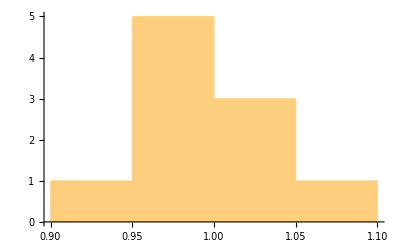

```mathematica
Histogram[Cauchy1[[5]]]
```